2.1 Index of fixed point

a)

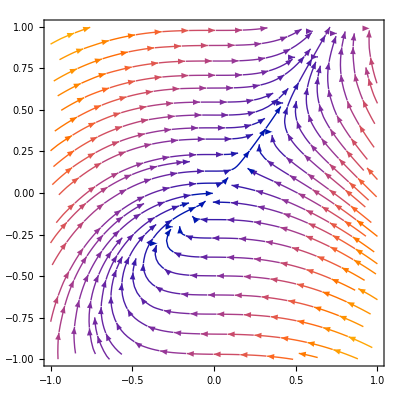

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y-x;
ydot = x^2;
P ={xdot,ydot};
lim = 1;
StreamPlot[P,{ x,-lim,lim},{y,-lim,lim}]
```

b)

r Cos[theta] (Sin[theta]+Cos[theta] (-1+r Sin[theta]))

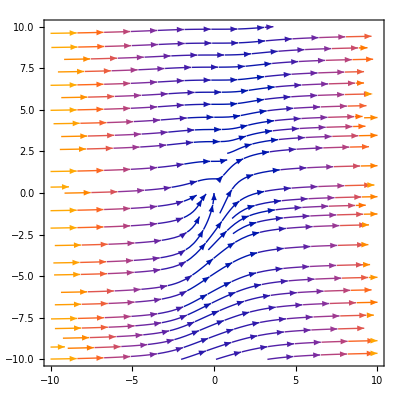

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.; theta=.;
lim = 10;
xdot = y-x;
ydot = x^2;
P ={xdot,ydot};
P =ToPolarCoordinates[{P}];
StreamPlot[P,{x,-lim,lim},{y,-lim,lim}]
```

c)

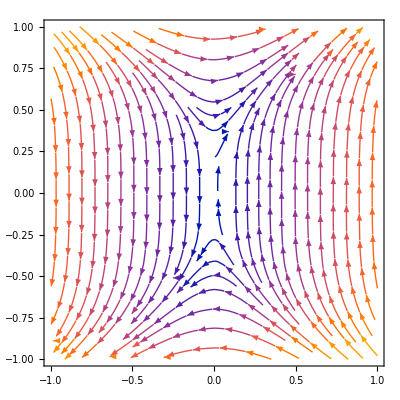

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y^3;
ydot = x;
P ={xdot,ydot};
lim = 1/1;
StreamPlot[P,{ x,-lim,lim},{y,-lim,lim}]
```

d)

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
n=.;
xdot =(x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]] ;
ydot = (x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
lim = 10;
P ={xdot,ydot};
Manipulate[StreamPlot[{(x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]],(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]]},{x,-lim,lim},{y,-lim,lim}],{n,0,5}]
```

2.2

```mathematica
xdot=.;ydot=.;y=.;x=.;sigma=.;
xdot = y;
ydot = -Sin[x]-sigma y
Dsolve[xdot,ydot]
```

-sigma y-Sin[x]

Dsolve[y,-sigma y-Sin[x]]

2.3

```mathematica
xdot=.;ydot=.;y=.;x=.;sigma=.;mu=.;xdot2=.;ydot2=.;

xdot = mu x - 5 y -x^3;
ydot = 5x+mu y+3y^3;
xdot2 = mu x+y-x^2;
ydot2 = -x+y mu + 2x^2;
mu=0;
ToPolarCoordinates[{xdot,ydot}]
```

{√((-x^3-5 y)^2+(5 x+3 y^3)^2),ArcTan[-x^3-5 y,5 x+3 y^3]}